# Variacijski račun

## Rayleigh - Ritzova metoda

Približek za ekstremalo funkcionala
               F[y] = (∫_a)^b f(x,y,y') dx,    y(a) = A,    y(b) = B
zapišemo kot vsoto koordinatnih funkcij
               y_n(x) = φ_0(x) + ∑_(i=1)^n a_i φ_i(x),
kjer koordinatne funkcije izberemo tako, da so zvezno odvedljive in zadoščajo sledečim napotkom:
- če so robni pogoji homogeni (torej y(a) = y(b) = 0), je φ_0(x) = 0, za φ_i(x) pa naj velja φ_i(a) = φ_i(b) = 0,
- če robni pogoji niso homogeni (torej y(a) = A in y(b) = B), izberemo φ_0(x) tako, da zadošča robnim pogojem, za φ_i(x) pa naj velja φ_i(a) = φ_i(b) = 0.

Na intervalu (0,1) je tako ustrezen izbor koordinatnih funkcij recimo:
               φ_1(x) = x^2-x,  φ_2(x) = x^3-x^2,  φ_3(x) = x^4-x^3 ...
Katero funkcijo je smiselno izbrati za koordinatno funkcijo φ_0(x), če robni pogoji niso homogeni?

1. Z uporabo Rayleigh-Ritzove metode poiščite prvih 6 zaporednih približkov za ekstremalo funkcionala
                F[y] =∫_0^2 (2x y+9 y^2+(y')^2)ⅆx,      y(0)=0,   y(2)=0.
     Na isti graf narišite dobljenih 6 približkov ter kandidata za ekstremalo, ki ga dobite kot rešitev Euler-Lagrangeove enačbe.
     Izračunajte še tabelo vrednosti danega funkcionala za dobljene približke po Rayleigh-Ritzovi metodi ter za kandidata za ekstremalo.

     Nalogo ponovite še za robne pogoje y(0)=1, y(2)=3, kjer dodate še koordinatno funkcijo φ_0(x), ki zadošča robnim pogojem.

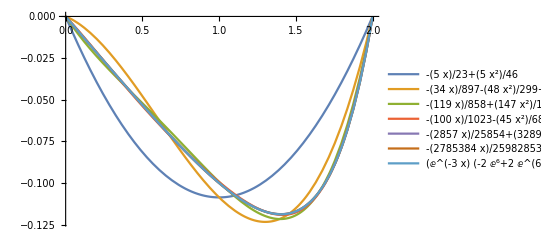

{-0.144928,-0.168859,-0.172416,-0.172806,-0.172836,-0.172838,-0.172838}

```mathematica
(* a) homogeni robni pogoji: *)
Clear[a,n,y,Y]
(* Koordinatne funkcije: *)
φ={x^2-2x,x^3-2x^2,x^4-2x^3,x^5-2x^4,x^6-2x^5,x^7-2x^6};
Y={};
(* Rayleigh-Ritzova metoda: *)
For[n=1,n≤Length[φ],n++,
y=Sum[a[i]φ[[i]],{i,1,n}];
F=Integrate[2x y+9y^2+D[y,x]^2,{x,0,2}];
koef=Flatten[Solve[Table[D[F,a[i]]==0,{i,1,n}],Table[a[i],{i,1,n}]]];
AppendTo[Y,Expand[y/.koef]];
]
(* Euler-Lagrangeova enačba: *)
Clear[f,y]
f=2x y[x]+9(y[x])^2+(y'[x])^2;
(*Nujno y pišemo z y[x], da zna odvajati po x*)
D[f,y[x]]-D[D[f,y'[x]],x]==0; 
ye=DSolveValue[{%,y[0]==0,y[2]==0},y[x],x];
AppendTo[Y,ye]; (*K seznamu dodamp še rešitev ekstremale preko EL enačbe*)
Plot[Y,{x,0,2},PlotLegends->"Expressions"] (*Nariše kar cel seznam funkcij*)
(* Tabela vrednosti funkcionala: *)
N[Table[Integrate[2x Y[[i]]+9Y[[i]]^2+D[Y[[i]],x]^2,{x,0,2}],{i,1,Length[Y]}]]
```

1+x

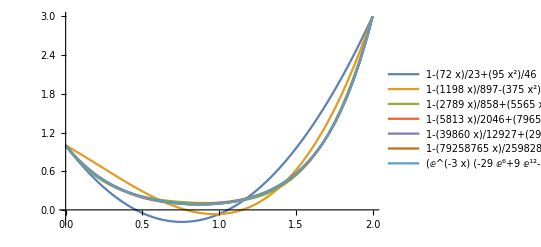

{37.0145,34.6213,33.3371,33.2981,33.2875,33.2873,33.2873}

```mathematica
(* b) nehomogeni robni pogoji: *)
Clear[a,n,y,Y]
(* Koordinatne funkcije: *)
(*Dodati moramo φ0, ki ustreza robnim pogojem*)
φ0=(3-1)/(2-0) (x-0)+1  (*Fi0=x+1*)
φ={x^2-2x,x^3-2x^2,x^4-2x^3,x^5-2x^4,x^6-2x^5,x^7-2x^6};
Y={};
(* Rayleigh-Ritzova metoda: *)
For[n=1,n≤Length[φ],n++,
y=φ0 + Sum[a[i]φ[[i]],{i,1,n}]; (*Dodamo še fi0*)
F=Integrate[2x y+9y^2+D[y,x]^2,{x,0,2}];
koef=Flatten[Solve[Table[D[F,a[i]]==0,{i,1,n}],Table[a[i],{i,1,n}]]];
AppendTo[Y,Expand[y/.koef]];
]
(* Euler-Lagrangeova enačba: *)
Clear[f,y]
f=2x y[x]+9(y[x])^2+(y'[x])^2;
(*Nujno y pišemo z y[x], da zna odvajati po x*)
D[f,y[x]]-D[D[f,y'[x]],x]==0; 
ye=DSolveValue[{%,y[0]==1,y[2]==3},y[x],x]; (*Popravimo robne pogoje*)
AppendTo[Y,ye]; (*K seznamu dodamp še rešitev ekstremale preko EL enačbe*)
Plot[Y,{x,0,2},PlotLegends->"Expressions"] (*Nariše kar cel seznam funkcij*)
(* Tabela vrednosti funkcionala: *)
N[Table[Integrate[2x Y[[i]]+9Y[[i]]^2+D[Y[[i]],x]^2,{x,0,2}],{i,1,Length[Y]}]]
```

## Metoda končnih razlik (diferenc)

Simetrični končni razliki za prvi in drugi odvod v notranjih delilnih točkah sta (kjer h=(b-a)/n in y_i ≈ y(x_i)):

               y'(x_i) ≈ (y_(i+1) - y_(i-1))/(2h),

               y''(x_i) ≈ (y_(i+1) - 2 y_i + y_(i-1))/h^2.

2. Z metodo simetričnih končnih razlik rešite diferencialno enačbo
	y'' + y' - 3y = x, y(0)=2, y(3)=1,
     kjer interval [0,3] razdelite na n=20 enako dolgih podintervalov.
     Določite vrednosti rešitve diferencialne enačbe v delilnih točkah.
    Dobljene rešitve primerjajte s točno rešitvijo diferencialne enačbe, ki jo dobite z ukazom DSolve[] ali DSolveValue[] .
     Preverite, kaj se dogaja,če spreminjate število podintervalov (n).

{2,1.35553,0.889242,0.550132,0.302302,0.120592,-0.0124928,-0.108955,-0.176822,-0.221206,-0.24503,-0.249521,-0.234517,-0.198658,-0.139463,-0.053331,0.064527,0.220224,0.421396,0.677468,1}

{2.,1.3549,0.888256,0.548944,0.300993,0.119199,-0.0139617,-0.110504,-0.178463,-0.222953,-0.246894,-0.251507,-0.236622,-0.200866,-0.141741,-0.0556218,0.0623105,0.218211,0.419768,0.676481,1.}

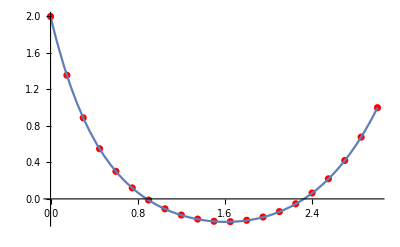

```mathematica
(* Izračun numerične rešitve: *)
a=0;b=3;A=2;B=1;
n=20;h=(b-a)/n;
xi=Table[a+i h,{i,0,n}];(*Notranje točke vključno z a na zečetku in b na koncu*)
(* Sistem enačb v notranjih točkah:
(2-h)Subscript[y, i-1] - (4+6h^2)Subscript[y, i] + (2+h)Subscript[y, i+1] = 2 h^2 Subscript[x, i] *)
U=DiagonalMatrix[Table[2-h,n-2],-1]+DiagonalMatrix[Table[-4-6h^2,n-1]]+DiagonalMatrix[Table[2+h,n-2],1];
v=2h^2Take[xi,{2,-2}];v[[1]]=v[[1]]-(2-h)A;v[[-1]]=v[[-1]]-(2+h)B;
u=N[LinearSolve[U,v]];
yi=Join[{A},u,{B}]
(* Izračun točne rešitve: *)
Clear[y,x]
sol=DSolveValue[{y''[x]+y'[x]-3y[x]==x,y[0]==2,y[3]==1},y[x],x];
yti=Table[N[sol/.x->xi[[i]]],{i,1,Length[xi]}]
(* Grafična predstavitev: *)
slika1=ListPlot[yi,PlotStyle->Red,DataRange->{0,3}];
slika2=Plot[sol,{x,0,3}];
Show[slika1,slika2,PlotRange->All]
```

### Primeri nalog za preverjanje

3. Poiščite ekstremalo funkcionala
	∫_1^2 y^2 y'^2 ⅆx,      y(1)=1,     y(2)=2     
      Koliko je y(3)?

Rezultat: 2.64575

```mathematica
f=y[x]^2*y'[x]^2;
Clear[x,y]
DSolveValue[{D[f,y[x]]-D[D[f,y'[x]],x]==0,y[1]==1,y[2]==2},y[x],x]
%/. x-> 3//N
```

DSolveValue::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

√(-2+3 x)

2.64575

4. Poiščite ekstremalo funkcionala
	∫_1^2 (y'^2+x^2 y)ⅆx,
      pri pogojih      ∫_1^2 xyⅆx=3,  y(1)=1,   y(2)=2     
      Koliko je y(3)?

Rezultat: -3.51961

```mathematica
Clear[x,y]
f=y[x] x ^2+y'[x]^2 +  L x y[x];
Y= DSolveValue[{D[f,y[x]]-D[D[f,y'[x]],x]==0,y[1]==1,y[2]==2},y[x],x]
(*Lambdo pa določimo z integralskim pogojem*)
Solve[Integrate[x Y, {x,1,2}]==3,L]
Y/. % /. x-> 3 //N
```

1/24 (14+12 L+9 x-14 L x+2 L x^3+x^4)

{{L→-585/68}}

{-3.51961}

5. Z metodo simetričnih končnih razlik rešite diferencialno enačbo
	x^2 y'' + 2x y' - 6y = x, y(1)=4, y(3)=-1,
      kjer interval [1,3] razdelite na n=12 enako dolgih podintervalov.
      Določite vrednosti rešitve diferencialne enačbe v delilnih točkah.
      Določite vrednost rešitve v drugi notranji delilni točki (y_2).

Rezultat: y_2=1.41272

```mathematica
(*1. način: priredimo rešitev od gornje predstavitve, z matrikami*)
(*Najprej treba ugotoviti kako se glasi enačba za notranje točke y_(i-1), y_i,y_(i+1) in nato pogledati še, akko je treba popraviti prvi in zandji element vektroja desnih strani v  -DN*)

(* 2. način *)
a=1;A=4;b=3;B=-1;
n=12 ;h=(b-a)/n;
x[i_]:= a+ i h

(*Generiramo seznam enačb v vsaki notranji točki - torej naše približke vstavimo v DE*)resitev=Solve[Table[x[i]^2*(y[i+1]-2y[i]+y[i-1])/h^2+2 x[i]*(y[i+1]-y[i-1])/(2 h)-6 y[i]==x[i],{i,1,n-1} ]/.{y[0]-> A,y[n]-> B}, Table[y[i],{i,1,n-1}]]
215780464315/152741226249//N
y[2]/.resitev//N
```

{{y[1]→5779389832951/2443859619984,y[2]→215780464315/152741226249,y[3]→219515377067/271539957776,y[4]→120824923145/305482452498,y[5]→230773793503/2443859619984,y[6]→-4694194263/33942494722,y[7]→-800904651677/2443859619984,y[8]→-74687836895/152741226249,y[9]→-171505375465/271539957776,y[10]→-116353458305/152741226249,y[11]→-2159444457503/2443859619984}}

1.41272

{1.41272}